```mathematica
<<"/Users/raina/Documents/MathematicaNB/Dynamica1.m"
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

```mathematica
sysCI2EqNoise=DynamicalSystem[{
qa A(1-A-B)-qb A B+n(-A (1-na)+((1-A-B)na)),
qb B(1-A-B)-qa B A+n(-B na+((1-A-B)(1-na)))},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{qa,0,10},{qb,0,10},{n,0,1},{na,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{qa,qb,n,na}]

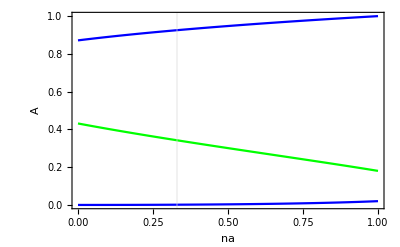

```mathematica
DisplayBifurcationDiagram[sysCI2EqNoise/.{qa->1,qb->0.92, n->0.1},na,StateVariables->{A},GridLines->{{0.33},{}}]
```

```mathematica
ER = EquilibriumBranches[sysCI2EqNoise/.{qa->1,qb->0.66, n->0.1},na];
ER[[1]][[3]][[4]]
```

{{1.,6.17494907650748×10^-26,1},{0.998855423389773,1.30855958231662×10^-6,0.987445747201732},{0.996236919787967,0.0000141078826206226,0.95899456434975},{0.99358383350834,0.0000409064034872001,0.930546595254499},{0.990895230134674,0.0000821555762245784,0.902101978171172},{0.988170132862429,0.00013832848367873,0.873660859696795},{0.985407519766028,0.000209921274274713,0.845223395429316},{0.9826063208362,0.000297454722161893,0.816789750691729},{0.979765414763344,0.000401475923815972,0.788360101329012},{0.976883625439884,0.000522560145848014,0.759934634586694},{0.973959718151113,0.000661312840681122,0.731513550081198},{0.970992395420053,0.000818371848955838,0.703097060873523},{0.967980292467262,0.000994409810066401,0.674685394659619},{0.964921972241215,0.00119013680517252,0.646278795092783},{0.961815919968747,0.00140630326044834,0.617877523255829},{0.958660537167872,0.00164370314231033,0.589481859303593},{0.955454135056967,0.00190317748101527,0.561092104299667},{0.952194927284514,0.00218561826446961,0.532708582275223},{0.94888102189217,0.00249197275049992,0.504331642542551},{0.945510412410379,0.0028232482533966,0.475961662301551},{0.942080967969805,0.00318051746949999,0.447599049584305},{0.938590422292888,0.00356492441724571,0.419244246591018},{0.935036361407245,0.00397769107979497,0.390897733480661},{0.931416209895626,0.00442012485360739,0.362560032691765},{0.927727215464661,0.00489362692464776,0.334231713883737},{0.923966431575467,0.00539970171608858,0.305913399607345},{0.92013069783167,0.0059399675783056,0.277605771835717},{0.916216617762511,0.00651616892485517,0.249309579515324},{0.9122205335678,0.00713019005849693,0.221025647331689},{0.908138497304115,0.00778407098116468,0.192754885928904},{0.903966237883487,0.00848002554366955,0.164498303878236},{0.899699123120921,0.00922046236823187,0.13625702176279},{0.89533211589795,0.0100080090741619,0.108032288837345},{0.89085972329576,0.0108455404601252,0.0798255028417434},{0.886275937279601,0.0117362114534787,0.0516382337020784},{0.881828467728096,0.0126313921427202,0.024976515123738},{0.879563197360738,0.0130990050749405,0.0116533386569365},{0.878419824557044,0.0133380044978198,0.00499376932987564},{0.877845407528224,0.0134588269624085,0.00166450237788399},{0.877558,0.0135196,0},{0.877557510447344,0.0135195720196723,0}}

```mathematica
combinedCIn = {}
For[i=1,i<=3,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

{}

```mathematica
theFile=File["/Users/raina/Documents/ant22exten/bif_basic/antci1_qa1.0_qb0.66_navary_1.txt"]
Export[theFile,combinedCIn,"Table"];
```

File[/Users/raina/Documents/ant22exten/bif_basic/antci1_qa1.0_qb0.66_navary_1.txt]

```mathematica
sysCI2EqNoisenoU=DynamicalSystem[{
qa A(1-A-B)-qb A B+n(-A(1-na)+(B na)),
qb B(1-A-B)-qa B A+n(-B na+(A (1-na)))
},
{{A,-0.01,1+0.01},{B,-0.01,1+0.01}},
{{qa,0,10},{qb,0,10},{n,0,1},{na,0,1}}]
```

DynamicalSystem[«2 ODEs»,{A,B},{qa,qb,n,na}]

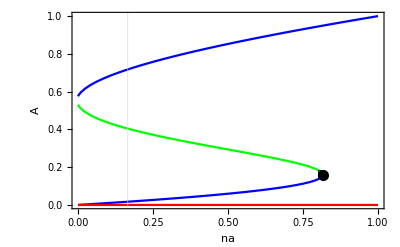

```mathematica
DisplayBifurcationDiagram[sysCI2EqNoisenoU/.{qa->1,qb->0.92, n->0.1},na,StateVariables->{A},GridLines->{{0.166},{}}]
```

```mathematica
ER = EquilibriumBranches[sysCI2EqNoisenoU/.{qa->1,qb->0.66, n->0.1},na];
ER[[1]][[4]][[4]]
```

{{0,0,1},{0,0,0.995256706650311},{0,0,0.966685278078883},{0,0,0.938113849507454},{0,0,0.909542420936025},{0,0,0.880970992364597},{0,0,0.852399563793168},{0,0,0.82382813522174},{0,0,0.795256706650311},{0,0,0.766685278078883},{0,0,0.738113849507454},{0,0,0.709542420936025},{0,0,0.680970992364597},{0,0,0.652399563793168},{0,0,0.62382813522174},{0,0,0.595256706650311},{0,0,0.566685278078882},{0,0,0.538113849507454},{0,0,0.509542420936025},{0,0,0.480970992364597},{0,0,0.452399563793168},{0,0,0.42382813522174},{0,0,0.395256706650311},{0,0,0.366685278078882},{0,0,0.338113849507454},{0,0,0.309542420936025},{0,0,0.280970992364597},{0,0,0.252399563793168},{0,0,0.22382813522174},{0,0,0.195256706650311},{0,0,0.166685278078882},{0,0,0.138113849507454},{0,0,0.109542420936025},{0,0,0.0809709923645967},{0,0,0.0523995637931681},{0,0,0.0253546276418555},{0,0,0.0118321595661992},{0,0,0.0050709255283711},{0,0,0.00169030850945703},{0,0,0},{0,0,0}}

```mathematica
combinedCIn = {}
For[i=1,i<=4,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

{}

```mathematica
theFile=File["/Users/raina/Documents/ant22exten/bif_basic/antci2_qa1.0_qb0.66_navary_1.txt"]
Export[theFile,combinedCIn,"Table"];
```

File[/Users/raina/Documents/ant22exten/bif_basic/antci2_qa1.0_qb0.66_navary_1.txt]

```mathematica
sysDSEqNoise=DynamicalSystem[{
qa A (1-A)- qb A(1-A)+n((1-A)na-A(1-na))
},
{{A,-0.01,1+0.01}},
{{qa,0,10},{qb,0,10},{n,0,1},{na,0,1}}]
```

DynamicalSystem[«1 ODE»,{A},{qa,qb,n,na}]

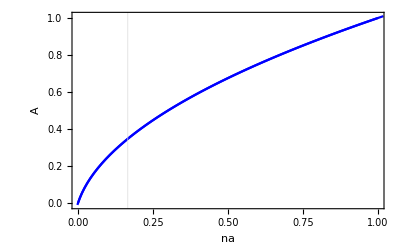

```mathematica
DisplayBifurcationDiagram[sysDSEqNoise/.{qa->1,qb->0.92, n->0.1},na,StateVariables->{A},GridLines->{{0.166},{}}]
```

```mathematica
ER = EquilibriumBranches[sysDSEqNoise/.{qa->1,qb->0.66, n->0.1},na];
ER[[1]][[3]][[4]]
```

Part::partw: Part 3 of {EquilibriumBranch[Stable,na,{{1.,1},...,«32»}],EquilibriumBranch[Unstable,na,{\*RowBox[{"{", RowBox[{RowBox[{"-", "0.01`"}], ",", "0.02433999999999999753929474932689927124`1…91003"}], "}"}]\),...,{-3.70465870074518×10^-25,0}}]} does not exist.

Part::partw: Part 4 of {EquilibriumBranch[Stable,na,{{1.,1},...,«32»}],EquilibriumBranch[Unstable,na,{\*RowBox[{"{", RowBox[{RowBox[{"-", "0.01`"}], ",", "0.02433999999999999753929474932689927124…1003"}], "}"}]\),...,{-3.70465870074518×10^-25,0}}]}⟦3⟧ does not exist.

{EquilibriumBranch[Stable,na,{{1.,1},...,{0.705882352941176,0}}],EquilibriumBranch[Unstable,na,{{-0.01,0.02434},...,{-3.70465870074518×10^-25,0}}]}⟦3⟧⟦4⟧

```mathematica
combinedCIn = {}
For[i=1,i<=2,++i,
val = ER[[1]][[i]][[4]];
combinedCIn=Join[combinedCIn,{{}},val];
]
combinedCIn;
```

{}

```mathematica
theFile=File["/Users/raina/Documents/ant22exten/bif_basic/antds_qa1.0_qb0.66_navary_1.txt"]
Export[theFile,combinedCIn,"Table"];
```

File[/Users/raina/Documents/ant22exten/bif_basic/antds_qa1.0_qb0.66_navary_1.txt]